## Derivation of Equations A1 - A3 and the plotting of Figure 2 in “The Population Genetics of Biological Noise” by DM Weinreich et al. Freely available under GNU General Public License (GPLv2)

June 4, 2025: Initial version

#### First, the derivations of Equations A1 - A3 in the appendix

Given phenotype z ~ N(z_0, σ^2) (Eqn 1 in ms) and fitness effect ∆r(z,z_0) = z_0^2 - z^2 (Eqn 2 in ms), we find the probability density function for ∆r(z,z_0) using the change-of-value technique shown at https://online.stat.psu.edu/stat414/lesson/22/22.3. 

These results match Matlab simulations (not shown; code available on request from daniel_weinreich@brown.edu).

Notation: fz[] is the pdf of z (Eq 1 in the ms), and v1[] and v2[] are the piece-wise inversions of the the function ∆r(z,z_0) =  z_0^2 -z^2 (Eq 2). f∆r[] is the pdf we seek.

```mathematica
fz[z_,z0_,σ_] :=PDF[NormalDistribution[z0,σ],z];
v1[r_,z0_]:=-Sqrt[z0^2-r];
v2[r_,z0_]:=Sqrt[z0^2-r];
```

The change-of-value technique recipe from the website tells us that f∆r(∆r,z0,σ) = fz(v1(∆r)) • |∂_(∆r) v1(∆r,z0)| + fz(v2(∆r)) • |∂_(∆r) v1(∆r,z0)|.  This is A1.

```mathematica
f∆r[∆r_,z0_,σ_]=fz[v1[∆r,z0],z0,σ]*Abs[∂_(∆r) v1[∆r,z0]]+fz[v2[∆r,z0],z0,σ]*Abs[∂_(∆r) v2[∆r,z0]]
```

(ⅇ^(-((-z0-√(-∆r+z0^2))^2)/(2 σ^2)))/(2 √(2 π) σ √Abs[-∆r+z0^2])+(ⅇ^(-((-z0+√(-∆r+z0^2))^2)/(2 σ^2)))/(2 √(2 π) σ √Abs[-∆r+z0^2])

But subsequent computations with this result in Mathematica are impractically slow. So I will take advantage of the fact that we can subtract r(z_0) = z_0^2 from every ∆r in the calculation and then add it back afterwards. Equivalently, we are shifting the pdf to the left (fig 2C) or down (left panel of figs 2A and B). Or put yet another way, we are calculating fitness effects relative to r(z_optimum), after which we find them relative to r(z_0) by addition. This trick has no impact on its integral, and we will recover the expectations of A1 in A2 and A3 by simply adding z_0^2.

Here’s that pdf: z_0 is set to zero in both calls to v1 and to v2, which are our connection to r(z).

```mathematica
fr[r_,z0_,σ_]=fz[v1[r,0],z0,σ]*Abs[D[v1[r,0], r]]+fz[v2[r,0],z0,σ]*Abs[D[v2[r,0], r]]
```

(ⅇ^(-(-√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])+(ⅇ^(-(√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])

Is that a pdf? Yes!

```mathematica
$Assumptions=Element[σ,PositiveReals];
FullSimplify[∫_-Infinity^0 fr[r,z0,σ]ⅆr]
```

1

What is the expected fitness effect over all noise? Here we’re using the trick: compute the expectation for the offset form of the pdf (fr[]) and then add z_0^2 back in to find the expectation of the pdf we want (f∆r[]). This is A2. Interestingly, it’s independent of z_0.

```mathematica
E∆r[z0_,σ_]=FullSimplify[∫_-Infinity^0 (fr[r,z0,σ]*r)ⅆr]+z0^2
```

-σ^2

Finally, what’s the expected fitness over only beneficial noise? First the numerator, noting that the limits of integration are correct for the shifted pdf. (Otherwise it’d be run from zero to r(z_optimum).)

```mathematica
Refine[FullSimplify[∫_(-(z0^2))^0 (fr[r,z0,σ]*r)ⅆr],Element[z0,Reals]]
```

1/2 (2 √(2/π) σ Abs[z0]+(z0^2+σ^2) (Erf[(z0-Abs[z0])/(√2 σ)]-Erf[(z0+Abs[z0])/(√2 σ)]))

And now the denominator -- the unweighted integral over the same interval -- needed to make our result a pdf.

```mathematica
Refine[FullSimplify[∫_(-(z0^2))^0 fr[r,z0,σ]ⅆr],Element[z0,Reals]]
```

Piecewise[{{-1/2 Erf[(√2 z0)/σ], z0<0}, {1/2 Erf[(√2 z0)/σ], z0>0}, {0, True}}]

Since Erf[x] = -Erf[-x], the denominator can be written 1/2 Abs[Erf[(z0 √2)/σ]]. This is A3; note  that I’m again adding z_0^2 back in to account for the offset between fr[] and f∆r[].

```mathematica
E∆rBeneficial[z0_,σ_]:=( Abs[z0] √(2/π) σ+1/2(z0^2+σ^2) (Erf[(z0-Abs[z0])/(√2 σ)]-Erf[(z0+Abs[z0])/(√2 σ)]))/(1/2 Abs[Erf[(z0 √2)/σ]])+z0^2;
```

#### Figure 2A bits and pieces. These were then pasted into Illustrator and massaged.

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->18,FontFamily->"Times New Roman"},AxesStyle->{{Thick,Black},{Thick,Black}},TicksStyle->{{Thick,Black},{Thick,Black}},FrameStyle->{{Thick,Black},{Thick,Black}}];
```

```mathematica
∆r[z_,z0_]:=z0^2-z^2;
z0:=-2;
lowNoise:=0.05;
highNoise:=0.4;
```

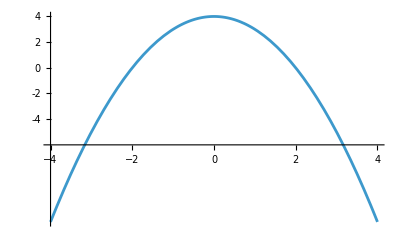

```mathematica
Plot[∆r[z,z0],{z,-4,4},AxesOrigin->{-4,-6},Ticks->{Automatic,{-4,-2,0,2,4}}]
```

Scale  to  fit  below  x - axis of the above : the full dynamic range above is from - 7 to + 11 = +18 
so  the  scaling  is  7/18.

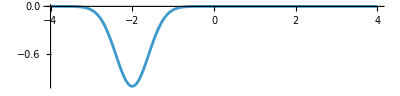

```mathematica
Plot[{-PDF[NormalDistribution[z0,highNoise],x]},{x,-4,4},PlotRange->All,AxesOrigin->{-4,0},AspectRatio->(7/18)/GoldenRatio]
```

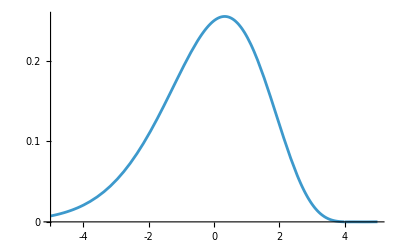

```mathematica
Plot[{f∆r[r,z0,highNoise]},{r,-5,5},PlotRange->All,Ticks->{{-4,-2,0,2,4},{0,.1,.2,.3}},AxesOrigin->{-5,0}]
```

#### Figure 2B

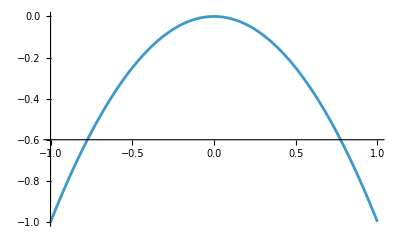

```mathematica
z0=0;
Plot[∆r[z,z0],{z,-1,1},AxesOrigin->{-1,-.6}]
```

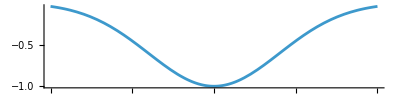

```mathematica
Plot[{-PDF[NormalDistribution[z0,highNoise],x]},{x,-1,1},PlotRange->All,AxesOrigin->{-1,0},AspectRatio->(7/18)/GoldenRatio]
```

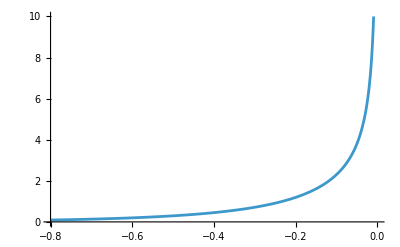

```mathematica
Plot[{f∆r[∆r,0,highNoise]},{∆r,-.8,0},PlotRange->{0,10},AxesOrigin->{-.8,0}]
```

#### Figure 2C

General::munfl: Exp[-3959.56] is too small to represent as a normalized machine number; precision may be lost.

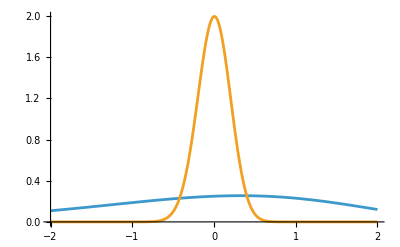

```mathematica
z0=-2;
Plot[{f∆r[∆r,z0,highNoise],f∆r[∆r,z0,lowNoise]},{∆r,-2,2},PlotRange->All,AxesOrigin->{-2,0}]
```

Here are the landmarks on the x-axis of Figure 2C.

```mathematica
E∆r[z0,lowNoise]
E∆r[z0,highNoise]
E∆rBeneficial[z0,lowNoise]
E∆rBeneficial[z0,highNoise]
```

-0.0025

-0.16

0.157077

1.11662

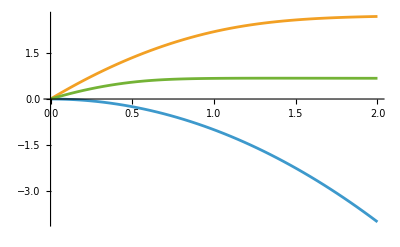

```mathematica
Plot[{E∆r[-2,σ],E∆rBeneficial[-2,σ],E∆rBeneficial[-1,σ]},{σ,0,2}]
```